## Exercises: Dynamic Computation

### Exercise1 Make a Manipulate that displays Graphics[{c,Disk[]}] and with a RadioButtonBar control for setting the value of c to Blue, Green or Blue.

```mathematica
Manipulate[Graphics[{c,Disk[]}],{c,{Blue,Green,Red}},ControlType-> RadioButtonBar]
```

### Exercise2 Use DynamicModule to modify this program to localize the dynamic variable:

```mathematica
Panel[Column[{Slider[Dynamic[n],{0,10,1},Appearance->"Labeled"],Dynamic[Range[n]]}]]
```

|

```mathematica
DynamicModule[{n},Panel[Column[{Slider[Dynamic[n],{0,10,1},Appearance->"Labeled"],Dynamic[Range[n]]}]]]
```

### Exercise3 Modify this program so that the checkbox controls are displayed in a 2×2 grid on the left side of the display rather than in a column above the display:

```mathematica
Manipulate[Grid[{{x11,x12},{x21,x22}},Dividers->All],{x11,{Black,White}},{x12,{Black,White}},{x21,{Black,White}},{x22,{Black,White}},ControlType->Checkbox]
```

```mathematica
Manipulate[Grid[{{x11,x12},{x21,x22}},Dividers->All],{x11,{Black,White}},{x12,{Black,White}},{x21,{Black,White}},{x22,{Black,White}},ControlType->Checkbox,ControlPlacement->Left]
```

## Exercises: Constructing User Interface

### Exercise1 Change this Manipulate program to use a Locator control rather than a pair of sliders for controlling the location of a circle in a graphic:

```mathematica
Manipulate[Graphics[Circle[{x,y}],Axes->True,PlotRange->10],{{x,0},-10,10},{{y,0},-10,10}]
```

```mathematica
Manipulate[Graphics[Circle[pt],Axes->True,PlotRange->10],{{pt,{0,0}},Locator}]
```

### Exercise2 Use TabView to set up a display with tabs to choose among displaying a graphic containing a disk, a circle or a triangle ( Graphics[Disk[]] , Graphics[Circle[]], Graphics[Triangle[]]).

```mathematica
TabView[{disk->Graphics[Disk[]],circle->Graphics[Circle[]],triangle->Graphics[Triangle[]]}]
```

123

### Exercise3 Modify this FormPage input to use the “String” interpreter and to apply StringLength to the string that is entered:

```mathematica
FormPage[{{"x","enter an integer:"}->"ComputedInteger"},FactorInteger[#x]&]
```

```mathematica
FormPage[{{"x","enter a string:"}->"String"},StringLength[#x]&]
```

### Exercise4 Modify this program so that, instead of inserting “MAX” in place of elements larger than 10, the program puts up a blocking dialog box with a button to insert “MAX” and a button to insert Nothing in place of those elements. (Inserting Nothing will have the effect of deleting those elements from the list):

```mathematica
Map[
If[#>10,"MAX",#]&,
Range[12]
]
```

```mathematica
Map[If[#>10,DialogInput[Row[{DefaultButton["delete element",DialogReturn[Nothing]],CancelButton["insert MAX",DialogReturn["MAX"]]}]],#]&,Range[12]]
```

{1,2,3,4,5,6,7,8,9,10,MAX,MAX}

## Exercises: Knowledge Representation

### Exercise1 Use Hold and InputForm to get ArgentinapopulationYear:2010 in InputForm format(formattedusingexplicitEntityandEntityPropertyexpressions).

```mathematica
Entity["Country","Argentina"][]//Hold //InputForm
```

Hold[Entity["Country", "Argentina"][EntityProperty["Country", "Population", {"Date" -> DateObject[{2010}]}]]]

### Exercise2 Use EntityValue to get a list consisting of the name and mass of the planet Jupiter.

```mathematica
EntityValue[Entity["Planet", "Jupiter"], {"Name","Mass"}]
```

{Jupiter,1.898×10^27 kg}

### Exercise3 Find the list of entities represented by halogens.

```mathematica
EntityClass["Element","Halogen"]["Properties"]
```

{adiabatic index,allotropes,allotropic multiplicities,alternate names,atomic mass,atomic number,atomic radius,atomic symbol,block,Bohr model plot,boiling point T_b,Brinell hardness,bulk modulus,CAS number,color,common compound names,covalent radius,critical pressure p_c,critical temperature T_c,crust abundance,crust molar abundance,Bravais lattice,lattice schematic,Curie point,Debye characteristic temperature,decay mode,discoverers,discovery country,discovery date,electrical conductivity,electrical type,electron affinity,electron count,electronegativity,electronic configuration,electron shell configuration,entity classes,entity type list,molar heat of fusion Δ_fusH,gas atomic multiplicities,group,half-life,human abundance,human molar abundance,icon color,image,ionization energies,isotope abundances,isotope half-lives,isotope lifetimes,known isotopes,known oxidation states,lattice angles,lattice constants,Lewis dot structure,liquid density,magnetic type,mass density,mass magnetic susceptibility,melting point T_m,memberships,meteorite abundance,meteorite molar abundance,Mohs hardness,molar heat capacity,molar magnetic susceptibility,molar mass,molar radioactivity,molar volume,most common oxidation states,name,Néel point,number of neutrons per isotope,neutron cross-section,neutron mass absorption,nuclear diameter,nuclear radius,ocean abundance,ocean molar abundance,orbital occupation list,origins,period,phase at STP,Poisson ratio,price,proton count,refractive index,resistivity,series,shear modulus,short electronic configuration,solar abundance,solar molar abundance,molar heat of solidification,sound speed,space group,IUCr space group number,specific heat of fusion Δ_fush,specific heat capacity c_p,specific ionization energies,specific radioactivity,specific heat of solidification,stable isotopes,superconducting point,tensile yield strength,term symbol,thermal conductivity,thermal expansion,threshold frequency,ultimate tensile strength,universe abundance,universe molar abundance,unstable isotopes,valence,valence electron count,van der Waals radius,molar heat of vaporization Δ_vapH,Vickers hardness,volume magnetic susceptibility,work function,Young modulus}

```mathematica
Manipulate[x,{x,{1,2,3},ControlType->RadioButtonBar}]
```

```mathematica
Manipulate[{x,y},Row[{Control[{x,{0,1}}],Control[{y,{0,1}}]}]]
```

```mathematica
MenuView[{1->"one",2->"two",3->"three"}]
```

```mathematica
CreatePalette[{x,0,10}]
```

```mathematica
LocalTime[Entity["Country","CostaRica"]]
```

Tue 21 Apr 2026 04:59:26GMT-6

```mathematica
EntityList[EntityClass["Cloud","CloudTypes"]]
```

{altocumulus,altostratus,asperitas,cirrocumulus,cirrus,cirrostratus,cumulonimbus,cumulus,lenticular,nimbostratus,stratocumulus,stratus}

## Exercises: Making Plots of Data

### Exercise1 Modify this input so that the vertical scale is logarithmic and so the data is shown with plot markers with style Style[“■”,Large,Blue] joined by straight lines. Lines joining plot markers can be specified using the option Joined→True:

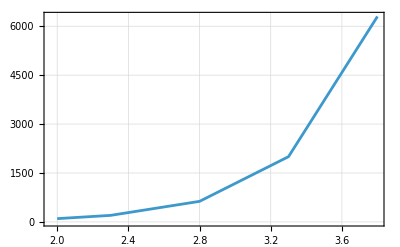

```mathematica
ListLinePlot[{{2,100},{2.3,200},{2.8,630},{3.3,2000},{3.8,6300}},Frame->True,GridLines->Automatic]
```

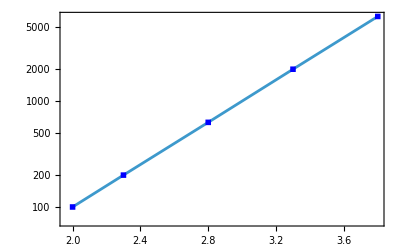

```mathematica
ListLinePlot[{{2,100},{2.3,200},{2.8,630},{3.3,2000},{3.8,6300}},Frame->True,GridLines->Automatic, ScalingFunctions->"Log", PlotMarkers -> Style["■",Large,Blue], Joined->True]
```

### Exercise2 Modify this input to show a callout label above each bar rather than a label below each bar:

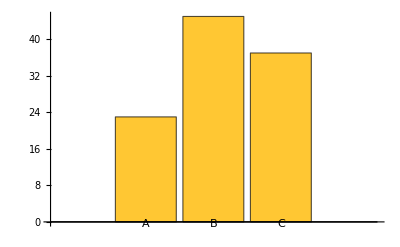

```mathematica
BarChart[{23,45,37},ChartLabels->{"A","B","C"}]
```

```mathematica
BarChart[{23,45,37},ChartLabels->Callout[{"A","B","C"}]]
```

-Graphics-

### Exercise3 This input uses Disk graphics primitives to construct a type of bubble chart. Use BubbleChart to make a bubble chart for the same data:

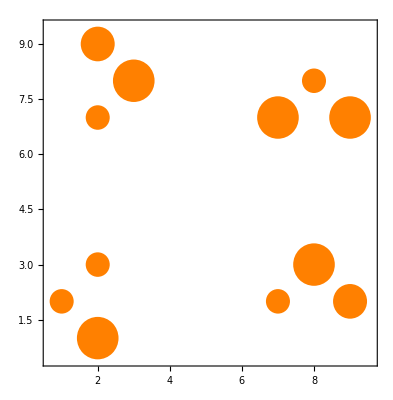

```mathematica
Graphics[{Orange,Apply[Disk[{#1,#2},Sqrt[#3]/3]&,{{1,2,1},{2,1,3},{2,3,1},{2,7,1},{3,8,3},{2,9,2},{7,2,1},{8,3,3},{9,2,2},{7,7,3},{9,7,3},{8,8,1}},{1}]},Frame->True]
```

```mathematica
BubbleChart[{{1,2,1},{2,1,3},{2,3,1},{2,7,1},{3,8,3},{2,9,2},{7,2,1},{8,3,3},{9,2,2},{7,7,3},{9,7,3},{8,8,1}}]
```

-Graphics-

## Exercises: Function Visualization

### Exercise1 Make a plot of the functions Exp[x], Exp[2x] and x^5, all on the same plot, for 1<x<10, and with a logarithmic vertical scale. Include the options GridLines→Automatic and Frame→True so that the plot is drawn with grid lines and a frame.

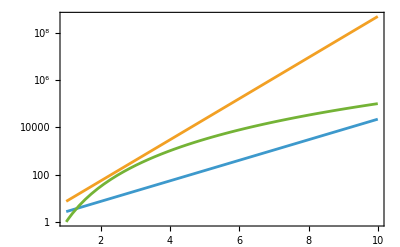

```mathematica
Plot[{Exp[x], Exp[2x], x^5},{x,1,10},ScalingFunctions->"Log", GridLines->Automatic,Frame->True]
```

### Exercise2 Change this input so that the vertical range goes from -6 to +6 and uses light gray shading rather than light red shading between the line and the axis:

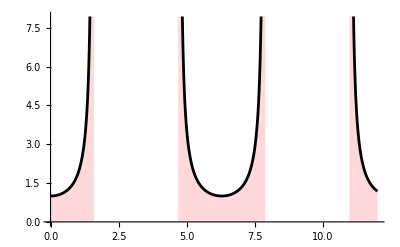

```mathematica
Plot[1/Cos[x],{x,0,12},PlotStyle->Black,Filling->{1->{Axis,LightRed}},PlotRange->{0,Automatic}]
```

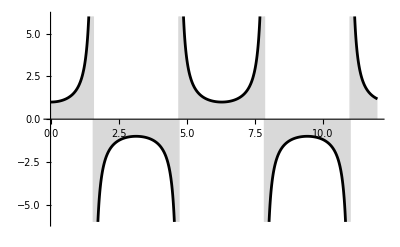

```mathematica
Plot[1/Cos[x],{x,0,12},PlotStyle->Black,Filling->{1->{Axis,LightGray}},PlotRange->{-6,6}]
```

#### Exercise3 Make a Manipulate to control a parametric plot of {xCos[t],(1-x)Sin[t]} for 0<t<2π, with a slider to control for x in the range -5<x<6, and with both the vertical and horizontal ranges in the plot fixed at -6 to 6.

```mathematica
Manipulate[ParametricPlot[{x Cos[t],(1-x)Sin[t]},{t,0,2Pi}, PlotRange->6],{x,-5,6}]
```

```mathematica
Manipulate[ParametricPlot[{x Cos[t],(1-x) Sin[t]},{t,1,5},PlotRange->6],{x,-5,6}]
```

## Exercises: Labeling Plots

### Exercise1 Add a frame and frame labels x and y for the horizontal and vertical scales in this plot, with all of the labels (including tick labels) given in 16 point font:

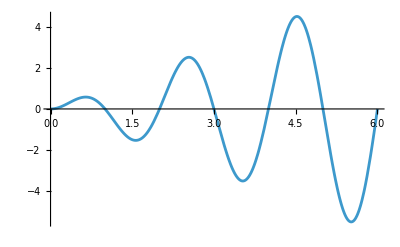

```mathematica
Plot[x Sin[π x],{x,0,6}]
```

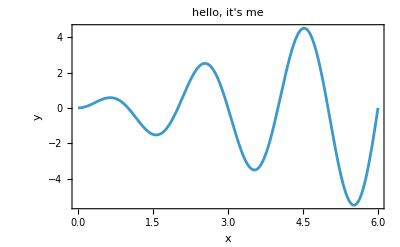

```mathematica
Plot[x Sin[π x],{x,0,6}, Frame->True, LabelStyle->16,FrameLabel->{"x", "y"}, PlotLabel->"hello, it's me" ]
```

### Exercise2 Add callout labels to the lines in this plot to label each line with the mathematical expression for the corresponding function. That is, the plot of Sqrt[x]Cos[x] should be labeled with xcos(x) and the plot of Sin[x] should be labeled with sin(x):

```mathematica
Plot[{Callout[Sqrt[x] Cos[x]],Callout[Sin[x]]},{x,0,5}]
```

-Graphics-

### Exercise3 Change this bar chart so that the bars start on the left side of the chart and extend to the right, and add a frame and labels in 12 point font with label A for the first bar, B for the second bar, C for the third bar, D for the fourth bar and E for the fifth bar:

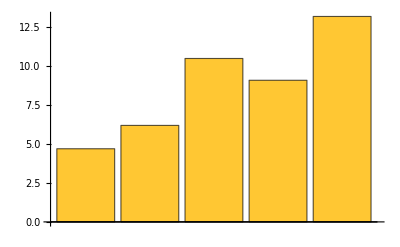

```mathematica
BarChart[{4.7,6.2,10.5,9.1,13.2}]
```

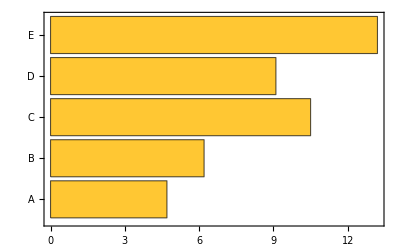

```mathematica
BarChart[{4.7,6.2,10.5,9.1,13.2}, BarOrigin->Left, Frame->True,LabelStyle->16, ChartLabels->{"A","B","C","D", "E"}]
```

```mathematica
data1 = {1,2,3,4,5,6};
data2={2,4,6,8,10};
```

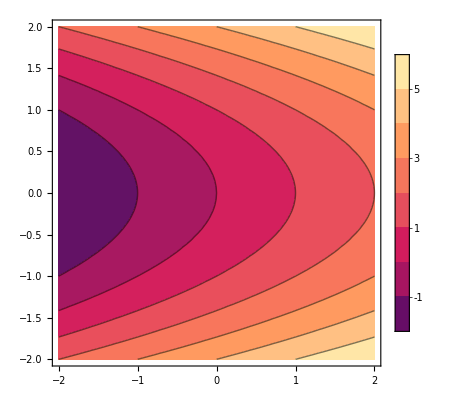

```mathematica
ContourPlot[x+y^2,{x,-2,2},{y,-2,2},PlotLegends->Automatic]
```

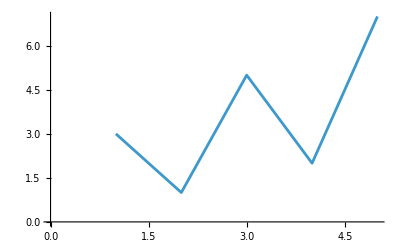

```mathematica
ListLinePlot[Tooltip[{3,1,5,2,7}]]
```

```mathematica
ListLinePlot[Tooltip/@{3,1,5,2,7}]
```

-Graphics-

```mathematica
ListLinePlot[{3,1,5,2,7},LabelStyle->Tooltip]
```

-Graphics-

```mathematica
ListLinePlot[{3,1,5,2,7},PlotLabels->Tooltip]
```

-Graphics-

```mathematica
BarChart[{1,Callout[2,"A"],3}]
```

-Graphics-

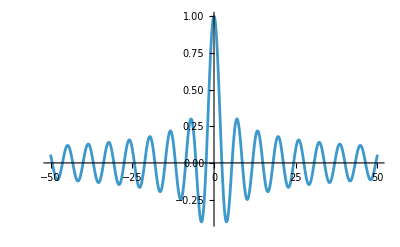

```mathematica
Plot[BesselJ[0,x],{x,-50,50},PlotRange->All]
```